## Plot of Bootstrapped Variance in May’s Harvesting Model

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_bootstrap/model_may"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
imgs=400; (* image size *)
{padLeft,padRight,padBottom,padTop}={60,30,10,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
bl=0.15;
bh=0.28;
(* realisation nuber for individual trajectory and power spectrum evolution *)
relNum=1;
```

## Import Data

```mathematica
ewsStd=Import["data_export/sim1_ews.csv"];
ewsBoot=Import["data_export/sim1_ews_boot.csv"];
```

## Trajectory Plots

```mathematica
(* columns *)
ewsStd[[1]]
```

{,Time,State variable,Smoothing,Residuals,Standard deviation,Variance}

```mathematica
(* Extract info *)
tVals = ewsStd[[2;;,2]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
rw=0.5;
windowComps=rw*tmax/dt2-1;
xVals = ewsStd[[2;;,3]];
```

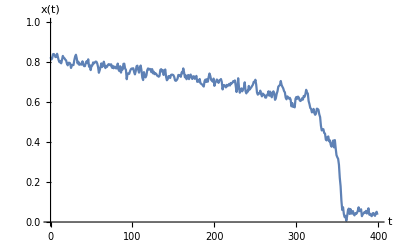

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[Transpose[{tVals,xVals}],
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tVals[[-1]]},{0,1}}]
```

## Bifurcation diagram

### Specifications

```mathematica
(* Import data *)
rawdata=Import["../../may_harvest_model/bifurcation_data/fold.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of mu *)
bVals=fulldata[[;;,1]];
tbifVals=(bVals-bl)*tmax /(bh-bl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections=Append[nodeSections,Cases[nodeSections[[7]],{_,x_,_,_}/;x<=0.75]];
nodeSections[[7]]=Cases[nodeSections[[7]],{_,x_,_,_}/; x>=0.65] ;*)(* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}];
```

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

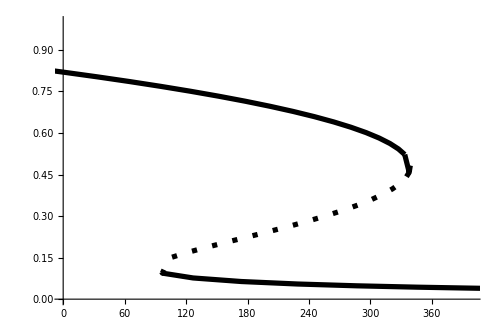

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tVals[[-1]]},{0,1}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

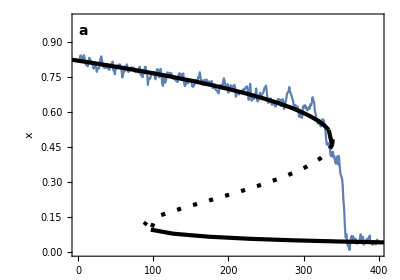

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajX=Show[{plotX,bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
AspectRatio->0.7,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->400,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]]}
]
```

## Variance

```mathematica
index=Position[ewsStd[[1]],"Variance"][[1,1]];
```

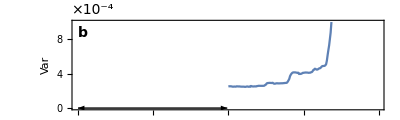

```mathematica
ymin=0;
ymax=0.001;
plotVar=ListLinePlot[ewsStd[[2;;,index]],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{Transpose[{Range[0,10,2]*10^(-4),Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight},{windowComps*dt2,ymin}]}],
Text[Style["×10^-4",14],indexPos],
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

## Variance from bootstrapped time-series

```mathematica
ewsBoot//Dimensions
```

{356,4}

```mathematica
ewsBoot[[1]]
```

{,Quantile,Time,Variance}

```mathematica
(* Extract quantile information *)
quant0p05=Cases[ewsBoot,{_,0.05,_,_}][[;;,{3,4}]];
quant0p25=Cases[ewsBoot,{_,0.25,_,_}][[;;,{3,4}]];
quant0p5=Cases[ewsBoot,{_,0.5,_,_}][[;;,{3,4}]];
quant0p75=Cases[ewsBoot,{_,0.75,_,_}][[;;,{3,4}]];
quant0p95=Cases[ewsBoot,{_,0.95,_,_}][[;;,{3,4}]];
```

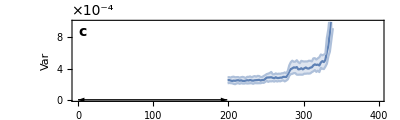

```mathematica
plotVarBoot=ListLinePlot[{quant0p5,quant0p05,quant0p95},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{1->{2},1->{3}}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
FrameLabel->{{"Var",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Transpose[{Range[0,10,2]*10^(-4),Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight},{windowComps*dt2,ymin}]}],
Text[Style["×10^-4",14],indexPos],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

## Combine plots

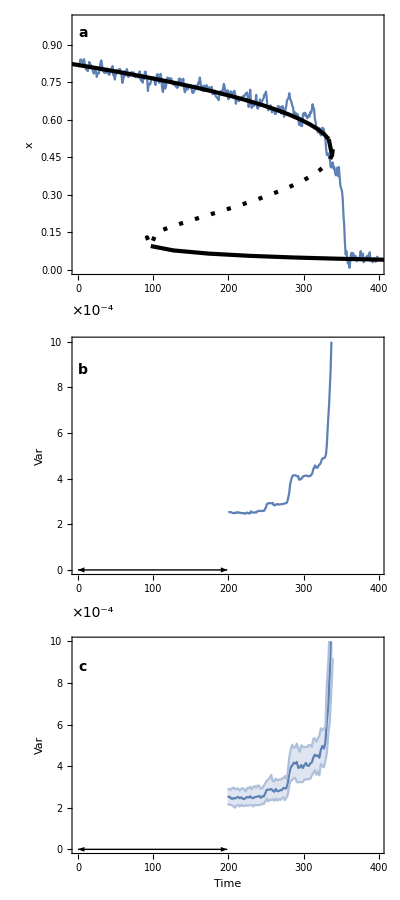

```mathematica
gridPlot=Grid[{{bifTrajX},{plotVar},{plotVarBoot}},Spacings->{-1.5,0}]
```

```mathematica
Export["figures/var_boot.png",gridPlot,ImageResolution->200];
```